```mathematica
(*X=10 Y=0.5 Yielding Physical states (and subsequently 3-entangled states) for t between 0 and 2pi*)
```

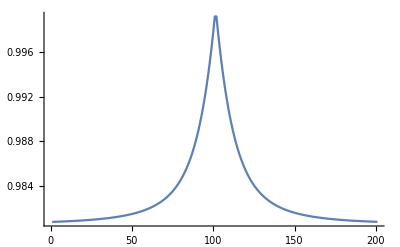

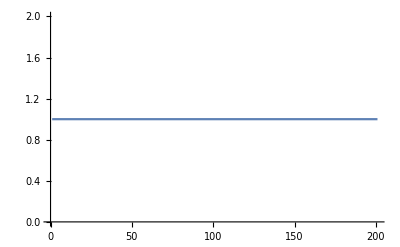

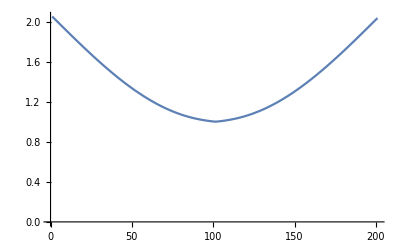

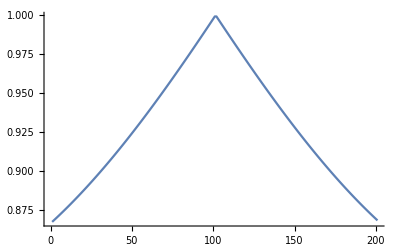

-Graphics-

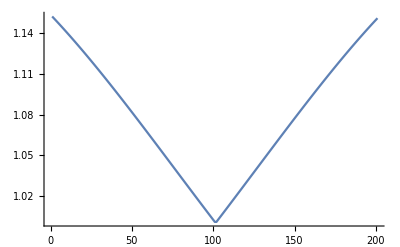

```mathematica
ListPlot[Table[Eigs[[1]],{t,3π/20,π/4,π/2000}],Joined->True,PlotRange->All]
ListPlot[Table[Eigs[[2]],{t,3π/20,π/4,π/2000}],Joined->True,PlotRange->All]
ListPlot[Table[Eigs[[3]],{t,3π/20,π/4,π/2000}],Joined->True,PlotRange->All]
ListPlot[Table[Eigs[[4]],{t,3π/20,π/4,π/2000}],Joined->True,PlotRange->All]
ListPlot[Table[Eigs[[5]],{t,3π/20,π/4,π/2000}],Joined->True,PlotRange->All]
ListPlot[Table[Eigs[[6]],{t,3π/20,π/4,π/2000}],Joined->True,PlotRange->All]
(*Checking first condition for Bona Fide C.M.; These eigenfunctions should be greater than 0 to be physical*)
```

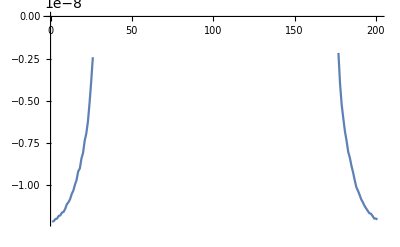

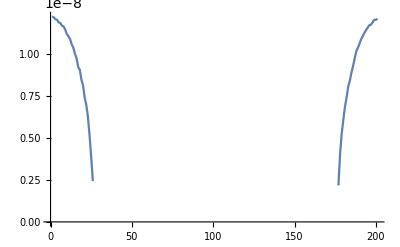

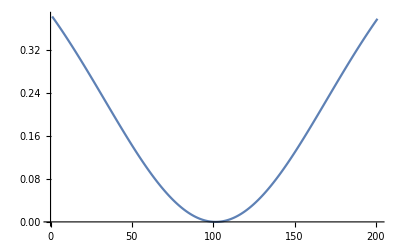

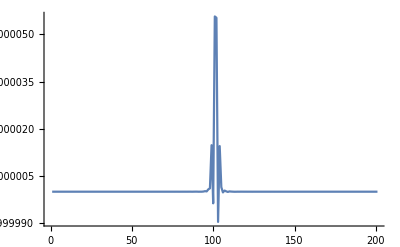

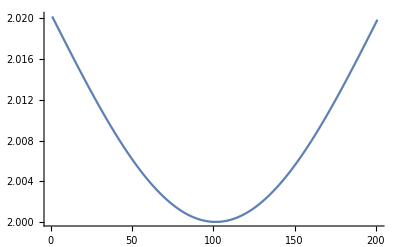

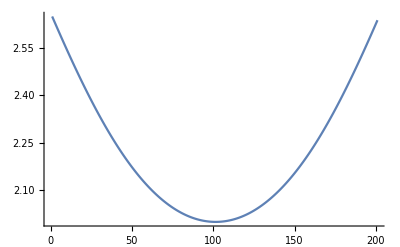

```mathematica
EigSymp=Eigenvalues[σ+ⅈ Σ];
ListPlot[Table[EigSymp[[1]],{t,3π/20,π/4,π/2000}],Joined->True,PlotRange->All]
ListPlot[Table[EigSymp[[2]],{t,3π/20,π/4,π/2000}],Joined->True,PlotRange->All]
ListPlot[Table[EigSymp[[3]],{t,3π/20,π/4,π/2000}],Joined->True,PlotRange->All]
ListPlot[Table[EigSymp[[4]],{t,3π/20,π/4,π/2000}],Joined->True,PlotRange->All]
ListPlot[Table[EigSymp[[5]],{t,3π/20,π/4,π/2000}],Joined->True,PlotRange->All]
ListPlot[Table[EigSymp[[6]],{t,3π/20,π/4,π/2000}],Joined->True,PlotRange->All]
(*Checking second condition for Bona Fide C.M.; These eigenfunctions should be also greater than 0 to be physical*)
```

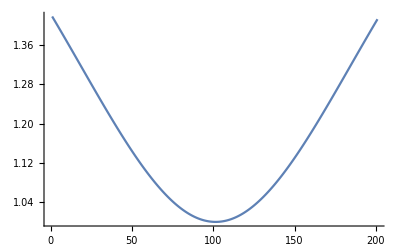

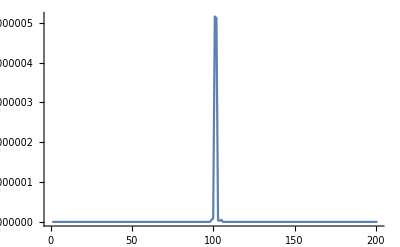

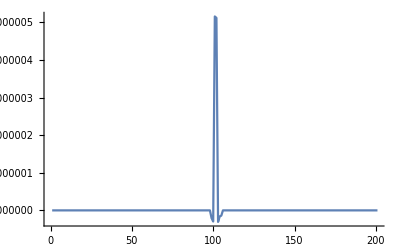

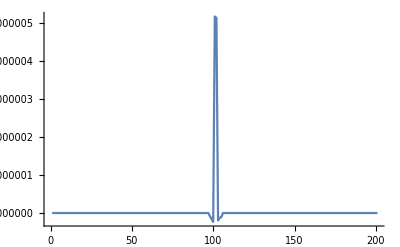

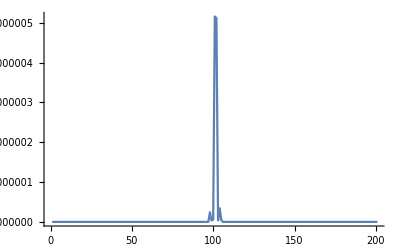

-Graphics-

```mathematica
SympEig=Eigenvalues[ⅈ Σ . σ];
ListPlot[Table[Abs[SympEig[[1]]],{t,3π/20,π/4,π/2000}],Joined->True,PlotRange->All]
ListPlot[Table[Abs[SympEig[[2]]],{t,3π/20,π/4,π/2000}],Joined->True,PlotRange->All]
ListPlot[Table[Abs[SympEig[[3]]],{t,3π/20,π/4,π/2000}],Joined->True,PlotRange->All]
ListPlot[Table[Abs[SympEig[[4]]],{t,3π/20,π/4,π/2000}],Joined->True,PlotRange->All]
ListPlot[Table[Abs[SympEig[[5]]],{t,3π/20,π/4,π/2000}],Joined->True,PlotRange->All]
ListPlot[Table[Abs[SympEig[[6]]],{t,3π/20,π/4,π/2000}],Joined->True,PlotRange->All]
(*Checking third condition for Bona Fide C.M.; These eigenfunctions should be also greater than or equal 1 (not zero) to be physical*)
```

```mathematica
V1=Table[Min[Abs[Eigenvalues[ⅈ Σ . σPT1]]],{t,3π/20,π/4,π/2000}];
V2=Table[Min[Abs[Eigenvalues[ⅈ Σ . σPT2]]],{t,3π/20,π/4,π/2000}];
V3=Table[Min[Abs[Eigenvalues[ⅈ Σ . σPT3]]],{t,3π/20,π/4,π/2000}];
(*Symplectic eigenvalues. If any are less than 1 then there exists some entanglement: NPT criterion*)
```

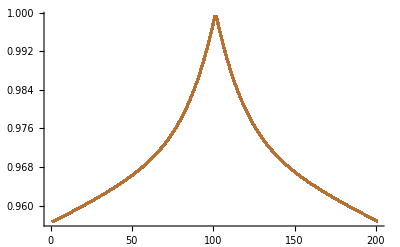

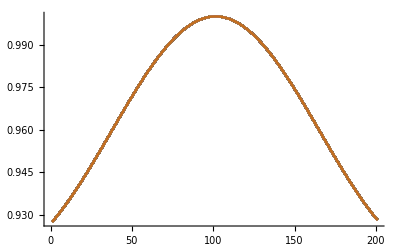

```mathematica
ListPlot[Table[V1,{t,3π/20,π/4,π/2000}],Joined->True,PlotRange->All]
ListPlot[Table[V2,{t,3π/20,π/4,π/2000}],Joined->True,PlotRange->All]
ListPlot[Table[V3,{t,3π/20,π/4,π/2000}],Joined->True,PlotRange->All]
```

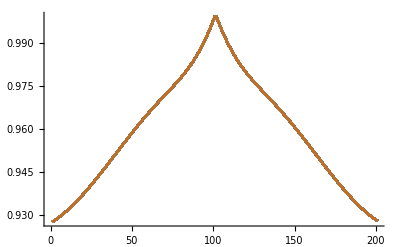

```mathematica
Clear[LogNeg1]
Clear[LogNeg2]
Clear[LogNeg3]
```

```mathematica
LogNeg1=Table[Max[0,-Log[Min[Abs[Eigenvalues[ⅈ Σ . σPT1]]]]],{t,3π/20,π/4,π/2000}];
LogNeg2=Table[Max[0,-Log[Min[Abs[Eigenvalues[ⅈ Σ . σPT2]]]]],{t,3π/20,π/4,π/2000}];
LogNeg3=Table[Max[0,-Log[Min[Abs[Eigenvalues[ⅈ Σ . σPT3]]]]],{t,3π/20,π/4,π/2000}];
```

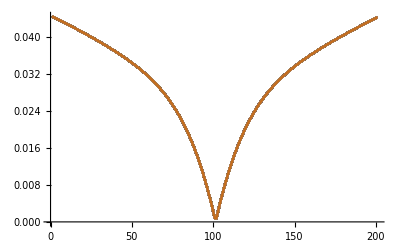

```mathematica
ListPlot[Table[LogNeg1,{t,3π/20,π/4,π/2000}],Joined->True,PlotRange->All]
```

```mathematica
LogNeg1[[100]]
LogNeg1[[101]]
LogNeg1[[102]]
LogNeg1[[103]]
LogNeg1[[104]]
(*ALL non-zero. Therefore, bipartite entanglement between crystal and emitted field for 0 < t < 4*)
```

0.00228909

0.000779167

0.000776274

0.00228631

0.00373708

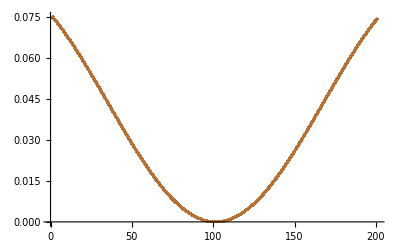

```mathematica
ListPlot[Table[LogNeg2,{t,3π/20,π/4,π/2000}],Joined->True,PlotRange->All]
```

```mathematica
LogNeg2[[95]]
LogNeg2[[96]]
LogNeg2[[97]]
LogNeg2[[98]]
LogNeg2[[99]]
LogNeg2[[100]]
LogNeg2[[101]]
LogNeg2[[102]]
LogNeg2[[103]]
LogNeg2[[104]]
(*some very small values! 10^-6. Do we consider this as 0? Lets investigate further.*)
```

0.000520314

0.00037277

0.000249681

0.000151119

0.0000771407

0.00002779

3.09581×10^-6

3.07263×10^-6

0.0000277205

0.0000770248

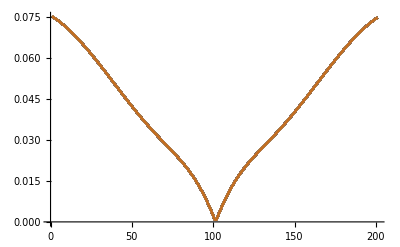

```mathematica
ListPlot[Table[LogNeg3,{t,3π/20,π/4,π/2000}],Joined->True,PlotRange->All]
```

```mathematica
LogNeg3[[100]]
LogNeg3[[101]]
LogNeg3[[102]]
LogNeg3[[103]]
LogNeg3[[104]]
```

0.00228893

0.000779161

0.000776268

0.00228615

0.0037364

```mathematica
LogNeg123=Table[CubeRoot[(Max[0,-Log[Min[Abs[Eigenvalues[ⅈ Σ . σPT1]]]]])(Max[0,-Log[Min[Abs[Eigenvalues[ⅈ Σ . σPT2]]]]])(Max[0,-Log[Min[Abs[Eigenvalues[ⅈ Σ . σPT3]]]]])],{t,3π/20,π/4,π/2000}]//Chop;
```

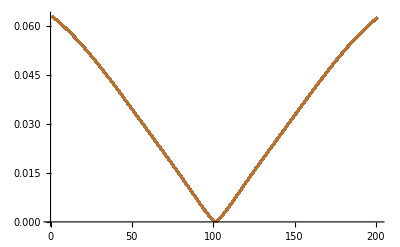

```mathematica
ListPlot[Table[LogNeg123,{t,3π/20,π/4,π/2000}],Joined->True,PlotRange->All]
```

```mathematica
LogNeg123[[100]]
LogNeg123[[101]]
LogNeg123[[102]]
LogNeg123[[103]]
LogNeg123[[104]]
```

0.000526091

0.000123408

0.000122795

0.000525227

0.00102456